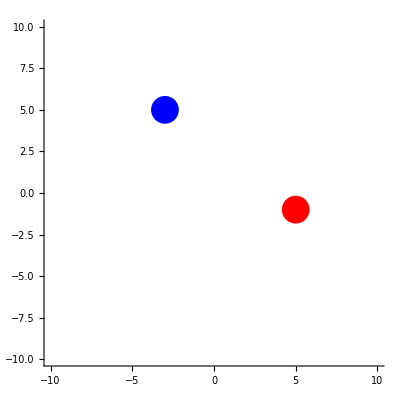

```mathematica
Graphics[{PointSize@0.05, Blue,Point[{{-3,5}}],Red,Point[{{5,-1}}]}, Axes->True, PlotRange->{{-10,10},{-10,10}}]
```

Going blue to red.
|a1-a2| = 8
|b1-b2| = 6
sqrt((a1-a3)^2 + (b1-b3)^2) = 5
sqrt((-3-a3)^2 + (5-b3)^2) = 5
|a1-a3|/|b1-b3|=8/6
|-3-a3|/|5-b3|=8/6

```mathematica
b3 = 10
```

10

```mathematica
b3
```

10

```mathematica
Clear@b3
```

```mathematica
|-3|
```

```mathematica
Abs[-3]
```

3

```mathematica
Clear[LENGTH,a1,b1,a2,b2]
```

```mathematica
LENGTH=5
a1 = 3
b1 = -5
a2= -3
b2 = 3
```

5

3

-5

-3

3

```mathematica
NSolveValues[Sqrt[({a1}-a3)^2+({b1}-b3)^2]=={LENGTH}&&Abs[3-a3]/Abs[-5-b3]==Abs[{a1}-{a2}]/Abs[{b1}-{b2}],{a3,b3}]
```

NSolveValues::ifun: Inverse functions are being used by NSolveValues, so some solutions may not be found; use Reduce for complete solution information.

{{0.,-9.},{0.,-1.},{6.,-9.},{6.,-1.}}

```mathematica
a
```

a

```mathematica
Solve[25-(25+b^2 + 10b) == (9((-3)b)^2)/16,b]
```

{{b→-160/97},{b→0}}